## Usage

## Initialize

```mathematica
$HistoryLength=1;
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

```mathematica
Needs["ErrorBarPlots`"]
```

## Generate global Har translation decay plots

### Reading In Parameters:

```mathematica
AALength=1717;
(* using 1717 AA because that's half of the smFLAG tag and the entire ORF of KDM5B*)
myStartTime=5;
myEndTime=65;
```

```mathematica
sampleSize = Length@onlyYellowSpots  ;
(* sampleSize usually uses the same # as sample size, in my case, number of cells*) 
repetitions = 30  ;(* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

### Reading In Files

```mathematica
(*YOU WILL GET AN ERROR if you don't have a W, Y, G, and P file for each cell!!! *)
```

```mathematica
analysisFolder = "/Volumes/MINI/_har TEMP use for global analysis/"
```

/Volumes/MINI/_har TEMP use for global analysis/

```mathematica
myFolders = {"/Volumes/MINI/_har TEMP use for global analysis/20180910_Har/Analysis",     "/Volumes/MINI/_har TEMP use for global analysis/20180926_harringtonine_TL_TA/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181024_har_TA/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181026_TLhar/Analysis",  "/Volumes/MINI/_har TEMP use for global analysis/20181027_TL_same cells as overnight_HAR/Analysis" };
```

```mathematica
myYellowOnlyFiles = FileNames["*ySpotNTime.m",myFolders];
cellCount = Length@myYellowOnlyFiles
myNTYellowOnlyFiles = FileNames["*NT*ySpotNTime.m",myFolders];
NTcellCount = Length@myNTYellowOnlyFiles
myTLYellowOnlyFiles = FileNames["*TL*ySpotNTime.m",myFolders];
TLcellCount = Length@myTLYellowOnlyFiles
myTAYellowOnlyFiles = FileNames["*TA*ySpotNTime.m",myFolders];
TAcellCount = Length@myTAYellowOnlyFiles
```

22

5

5

12

```mathematica
myWhiteFiles =FileNames["*wSpotNTime.m",myFolders];
Length@myWhiteFiles
myTAWhiteFiles =FileNames["*TA*wSpotNTime.m",myFolders];
Length@myTAWhiteFiles
myNTWhiteFiles =FileNames["*NT*wSpotNTime.m",myFolders];
Length@myNTWhiteFiles
myTLWhiteFiles =FileNames["*TL*wSpotNTime.m",myFolders];
Length@myTLWhiteFiles
```

22

12

5

5

```mathematica
myAllYellowFiles = FileNames["*gSpotNTime.m",myFolders];
Length@myAllYellowFiles
myTAAllYellowFiles = FileNames["*TA*gSpotNTime.m",myFolders];
Length@myTAAllYellowFiles
myNTAllYellowFiles = FileNames["*NT*gSpotNTime.m",myFolders];
Length@myNTAllYellowFiles
myTLAllYellowFiles = FileNames["*TL*gSpotNTime.m",myFolders];
Length@myTLAllYellowFiles
```

22

12

5

5

```mathematica
myPurpleFiles = FileNames["*brSpotNTime.m",myFolders];
Length@myPurpleFiles
myTAPurpleFiles = FileNames["*TA*brSpotNTime.m",myFolders];
Length@myTAPurpleFiles
myNTPurpleFiles = FileNames["*NT*brSpotNTime.m",myFolders];
Length@myNTPurpleFiles
myTLPurpleFiles = FileNames["*TL*brSpotNTime.m",myFolders];
Length@myTLPurpleFiles
```

22

12

5

5

### Yellow Only Har translation decay

```mathematica
onlyYellow = Table[Import[myYellowOnlyFiles⟦j⟧],{j,1,Length@myYellowOnlyFiles,1}];
TAonlyYellow = Table[Import[myTAYellowOnlyFiles⟦j⟧],{j,1,Length@myTAYellowOnlyFiles,1}];
NTonlyYellow = Table[Import[myTLYellowOnlyFiles⟦j⟧],{j,1,Length@myTLYellowOnlyFiles,1}];
TLonlyYellow = Table[Import[myNTYellowOnlyFiles⟦j⟧],{j,1,Length@myNTYellowOnlyFiles,1}];
```

#### ALL :

```mathematica
name = "ALL";
spotCount = Total[Transpose[onlyYellow],{2}]//#[[All,2]]&;
times = Total[Transpose[onlyYellow],{2}]//#[[All,1]]/cellCount&;
```

```mathematica
yelOnlySpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*);
```

{{-178,212},{-118,195},{-58,185},{2,176},{62,183},{122,200},{182,187},{242,188},{302,178},{362,158},{422,164},{482,160},{542,149},{602,136},{662,134},{722,122},{782,121},{842,128},{902,108},{962,106},{1022,107},{1082,97},{1142,108},{1202,84},{1262,91},{1322,91},{1382,84},{1442,86},{1502,86},{1562,76},{1622,72},{1682,73},{1742,78},{1802,67},{1862,58},{1922,59},{1982,66},{2042,57},{2102,52},{2162,50},{2222,54},{2282,46},{2342,55},{2402,52},{2462,42},{2522,50},{2582,36},{2642,32},{2702,42},{2762,33},{2822,34},{2882,39},{2942,34},{3002,30},{3062,32},{3122,28},{3182,28},{3242,33},{3302,28},{3362,26},{3422,29},{3482,25},{3542,32},{3602,36},{3662,21}}

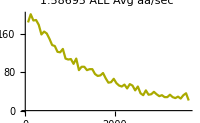
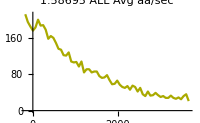
{{1.58695,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = yelOnlySpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{yelOnlyTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(myAvgAAperSec " Avg aa/sec" name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(myAvgAAperSec " Avg aa/sec" name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

#### EXPORT “ALL”:

```mathematica
Export[analysisFolder<>"_yOnlyGlobalTimePlot.tif",yelOnlyTimePlot];
yelOnlySpotCount>>analysisFolder<>"_OnlyGlobalTime.m"
```

#### TA:

```mathematica
name = "TA";
TAspotCount = Total[Transpose[TAonlyYellow],{2}]//#[[All,2]]&;
times = Total[Transpose[TAonlyYellow],{2}]//#[[All,1]]/TAcellCount&;
```

```mathematica
TAyelOnlySpotCount= Transpose[{times,TAspotCount}](*Combining Time with the # of spots*);
```

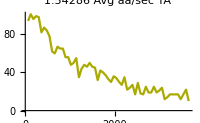
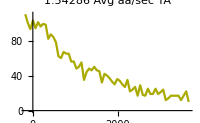
{{1.54286,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = TAyelOnlySpotCount;
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TAyelOnlyTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(name myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(name myAvgAAperSec " Avg aa/sec" ), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_yOnlyGlobalTimePlot.tif",TAyelOnlyTimePlot];
TAyelOnlySpotCount>>analysisFolder<>"_OnlyGlobalTime.m"
```

#### NT:

```mathematica
name = "NT";
NTspotCount = Total[Transpose[NTonlyYellow],{2}]//#[[All,2]]&;
times = Total[Transpose[NTonlyYellow],{2}]//#[[All,1]]/NTcellCount&;
```

```mathematica
NTyelOnlySpotCount= Transpose[{times,NTspotCount}](*Combining Time with the # of spots*);
```

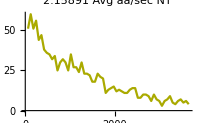
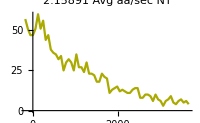
{{2.15891,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = NTyelOnlySpotCount;
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{NTyelOnlyTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(name myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(name myAvgAAperSec " Avg aa/sec" ), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_yOnlyGlobalTimePlot.tif",NTyelOnlyTimePlot];
NTyelOnlySpotCount>>analysisFolder<>"_OnlyGlobalTime.m"
```

#### TL:

```mathematica
name = "TL";
TLspotCount = Total[Transpose[TLonlyYellow],{2}]//#[[All,2]]&;
times = Total[Transpose[TLonlyYellow],{2}]//#[[All,1]]/TLcellCount&;
```

```mathematica
TLyelOnlySpotCount= Transpose[{times,TLspotCount}](*Combining Time with the # of spots*);
```

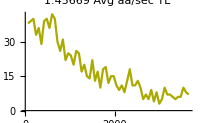
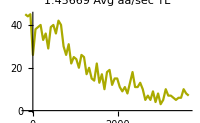
{{1.45669,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = TLyelOnlySpotCount;
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TLyelOnlyTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(name myAvgAAperSec " Avg aa/sec"), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Yellow,PlotLabel->(name myAvgAAperSec " Avg aa/sec" ), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_yOnlyGlobalTimePlot.tif",TLyelOnlyTimePlot];
TLyelOnlySpotCount>>analysisFolder<>"_OnlyGlobalTime.m"
```

### Yellow All Har translation decay

```mathematica
allYellow = Table[Import[myAllYellowFiles⟦j⟧],{j,1,Length@myAllYellowFiles,1}];
TAallYellow = Table[Import[myTAAllYellowFiles⟦j⟧],{j,1,Length@myTAAllYellowFiles,1}];
NTallYellow = Table[Import[myNTAllYellowFiles⟦j⟧],{j,1,Length@myNTAllYellowFiles,1}];
TLallYellow = Table[Import[myTLAllYellowFiles⟦j⟧],{j,1,Length@myTLAllYellowFiles,1}];
```

#### ALL:

```mathematica
name = "ALL";
spotCount = Total[Transpose[allYellow],{2}]//#[[All,2]]&;
```

```mathematica
yelAllSpotCount= Transpose[{times,spotCount}](*Combining Time with the # of spots*);
```

{{-178,303},{-118,289},{-58,266},{2,251},{62,266},{122,272},{182,279},{242,260},{302,255},{362,234},{422,229},{482,219},{542,211},{602,203},{662,187},{722,188},{782,182},{842,178},{902,161},{962,164},{1022,151},{1082,139},{1142,151},{1202,131},{1262,139},{1322,138},{1382,135},{1442,124},{1502,128},{1562,124},{1622,111},{1682,117},{1742,124},{1802,100},{1862,91},{1922,99},{1982,99},{2042,90},{2102,80},{2162,76},{2222,78},{2282,77},{2342,78},{2402,77},{2462,65},{2522,71},{2582,59},{2642,60},{2702,60},{2762,52},{2822,52},{2882,52},{2942,48},{3002,48},{3062,44},{3122,36},{3182,39},{3242,44},{3302,42},{3362,33},{3422,36},{3482,36},{3542,41},{3602,45},{3662,32}}

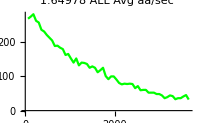
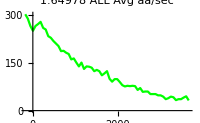
{{1.64978,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = yelAllSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{yelAllTimePlot=spotTime//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
yelAllTime = spotTime;
Export[analysisFolder<>"_yAllGlobalTimePlot.tif",yelAllTimePlot];
yelAllSpotCount>>analysisFolder<>"_yAllGlobalTime.m"
```

#### TA:

```mathematica
name = "TA";
TAspotCount = Total[Transpose[TAallYellow],{2}]//#[[All,2]]&;
```

```mathematica
TAyelAllSpotCount= Transpose[{times,TAspotCount}](*Combining Time with the # of spots*);
```

{{-178,172},{-118,161},{-58,143},{2,148},{62,146},{122,148},{182,152},{242,143},{302,146},{362,131},{422,131},{482,123},{542,118},{602,107},{662,98},{722,113},{782,108},{842,98},{902,92},{962,97},{1022,78},{1082,81},{1142,83},{1202,65},{1262,77},{1322,81},{1382,80},{1442,73},{1502,72},{1562,78},{1622,62},{1682,73},{1742,73},{1802,60},{1862,57},{1922,61},{1982,61},{2042,56},{2102,51},{2162,47},{2222,51},{2282,43},{2342,37},{2402,43},{2462,35},{2522,42},{2582,36},{2642,38},{2702,38},{2762,35},{2822,29},{2882,36},{2942,29},{3002,33},{3062,33},{3122,17},{3182,22},{3242,24},{3302,26},{3362,21},{3422,20},{3482,20},{3542,22},{3602,28},{3662,18}}

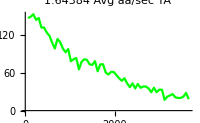
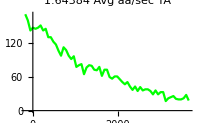
{{1.64384,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = TAyelAllSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TAyelAllTimePlot=spotTime//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_yAllGlobalTimePlot.tif",TAyelAllTimePlot];
TAyelAllSpotCount>>analysisFolder<>"_yAllGlobalTime.m"
```

#### TL:

```mathematica
name = "TL";
TLspotCount = Total[Transpose[TLallYellow],{2}]//#[[All,2]]&;
```

```mathematica
TLyelAllSpotCount= Transpose[{times,TLspotCount}](*Combining Time with the # of spots*);
```

{{-178,86},{-118,84},{-58,78},{2,77},{62,82},{122,85},{182,87},{242,84},{302,73},{362,74},{422,59},{482,56},{542,57},{602,54},{662,49},{722,45},{782,48},{842,49},{902,47},{962,42},{1022,49},{1082,38},{1142,42},{1202,41},{1262,45},{1322,37},{1382,40},{1442,37},{1502,34},{1562,33},{1622,32},{1682,34},{1742,33},{1802,21},{1862,22},{1922,23},{1982,23},{2042,23},{2102,20},{2162,18},{2222,19},{2282,21},{2342,23},{2402,23},{2462,19},{2522,16},{2582,13},{2642,17},{2702,15},{2762,12},{2822,14},{2882,12},{2942,11},{3002,12},{3062,6},{3122,9},{3182,10},{3242,13},{3302,10},{3362,7},{3422,10},{3482,10},{3542,9},{3602,9},{3662,7}}

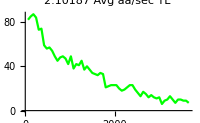
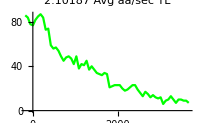
{{2.10187,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = TLyelAllSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TLyelAllTimePlot=spotTime//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_yAllGlobalTimePlot.tif",TLyelAllTimePlot];
TLyelAllSpotCount>>analysisFolder<>"_yAllGlobalTime.m"
```

#### NT:

```mathematica
name = "NT";
NTspotCount = Total[Transpose[NTallYellow],{2}]//#[[All,2]]&;
```

```mathematica
NTyelAllSpotCount= Transpose[{times,NTspotCount}](*Combining Time with the # of spots*)
```

{{-178,45},{-118,44},{-58,45},{2,26},{62,38},{122,39},{182,40},{242,33},{302,36},{362,29},{422,39},{482,40},{542,36},{602,42},{662,40},{722,30},{782,26},{842,31},{902,22},{962,25},{1022,24},{1082,20},{1142,26},{1202,25},{1262,17},{1322,20},{1382,15},{1442,14},{1502,22},{1562,13},{1622,17},{1682,10},{1742,18},{1802,19},{1862,12},{1922,15},{1982,15},{2042,11},{2102,9},{2162,11},{2222,8},{2282,13},{2342,18},{2402,11},{2462,11},{2522,13},{2582,10},{2642,5},{2702,7},{2762,5},{2822,9},{2882,4},{2942,8},{3002,3},{3062,5},{3122,10},{3182,7},{3242,7},{3302,6},{3362,5},{3422,6},{3482,6},{3542,10},{3602,8},{3662,7}}

{{-178,45},{-118,44},{-58,45},{2,26},{62,38},{122,39},{182,40},{242,33},{302,36},{362,29},{422,39},{482,40},{542,36},{602,42},{662,40},{722,30},{782,26},{842,31},{902,22},{962,25},{1022,24},{1082,20},{1142,26},{1202,25},{1262,17},{1322,20},{1382,15},{1442,14},{1502,22},{1562,13},{1622,17},{1682,10},{1742,18},{1802,19},{1862,12},{1922,15},{1982,15},{2042,11},{2102,9},{2162,11},{2222,8},{2282,13},{2342,18},{2402,11},{2462,11},{2522,13},{2582,10},{2642,5},{2702,7},{2762,5},{2822,9},{2882,4},{2942,8},{3002,3},{3062,5},{3122,10},{3182,7},{3242,7},{3302,6},{3362,5},{3422,6},{3482,6},{3542,10},{3602,8},{3662,7}}

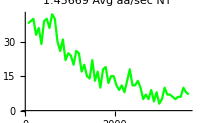
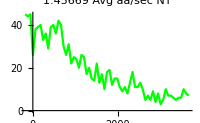
{{1.45669,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = NTyelAllSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{NTyelAllTimePlot=spotTime//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Green,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_yAllGlobalTimePlot.tif",NTyelAllTimePlot];
NTyelAllSpotCount>>analysisFolder<>"_yAllGlobalTime.m"
```

### White Har translation decay

```mathematica
white = Table[Import[myWhiteFiles⟦j⟧],{j,1,Length@myWhiteFiles,1}];
NTwhite = Table[Import[myNTWhiteFiles⟦j⟧],{j,1,Length@myNTWhiteFiles,1}];
TAwhite = Table[Import[myTAWhiteFiles⟦j⟧],{j,1,Length@myTAWhiteFiles,1}];
TLwhite = Table[Import[myTLWhiteFiles⟦j⟧],{j,1,Length@myTLWhiteFiles,1}];
```

#### ALL:

```mathematica
spotCount = Total[Transpose[white],{2}]//#[[All,2]]&;
times = Total[Transpose[white],{2}]//#[[All,1]]/cellCount&;
whiteSpotCount= Transpose[{times,spotCount}];(*Combining Time with the # of spots*)
```

{{-178,91},{-118,94},{-58,81},{2,75},{62,83},{122,72},{182,92},{242,72},{302,77},{362,76},{422,65},{482,59},{542,62},{602,67},{662,53},{722,66},{782,61},{842,50},{902,53},{962,58},{1022,44},{1082,42},{1142,43},{1202,47},{1262,48},{1322,47},{1382,51},{1442,38},{1502,42},{1562,48},{1622,39},{1682,44},{1742,46},{1802,33},{1862,33},{1922,40},{1982,33},{2042,33},{2102,28},{2162,26},{2222,24},{2282,31},{2342,23},{2402,25},{2462,23},{2522,21},{2582,23},{2642,28},{2702,18},{2762,19},{2822,18},{2882,13},{2942,14},{3002,18},{3062,12},{3122,8},{3182,11},{3242,11},{3302,14},{3362,7},{3422,7},{3482,11},{3542,9},{3602,9},{3662,11}}

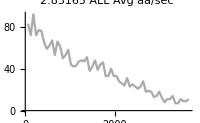
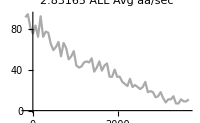
{{2.83165,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = whiteSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{whiteTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_wGlobalTimePlot.tif",whiteTimePlot];
whiteSpotCount>>analysisFolder<>"_wGlobalTime.m"
```

#### TA:

```mathematica
TAspotCount = Total[Transpose[TAwhite],{2}]//#[[All,2]]&;
```

```mathematica
name  = "TA";
TAwhiteSpotCount= Transpose[{times,TAspotCount}];(*Combining Time with the # of spots*)
```

{{-178,91},{-118,94},{-58,81},{2,75},{62,83},{122,72},{182,92},{242,72},{302,77},{362,76},{422,65},{482,59},{542,62},{602,67},{662,53},{722,66},{782,61},{842,50},{902,53},{962,58},{1022,44},{1082,42},{1142,43},{1202,47},{1262,48},{1322,47},{1382,51},{1442,38},{1502,42},{1562,48},{1622,39},{1682,44},{1742,46},{1802,33},{1862,33},{1922,40},{1982,33},{2042,33},{2102,28},{2162,26},{2222,24},{2282,31},{2342,23},{2402,25},{2462,23},{2522,21},{2582,23},{2642,28},{2702,18},{2762,19},{2822,18},{2882,13},{2942,14},{3002,18},{3062,12},{3122,8},{3182,11},{3242,11},{3302,14},{3362,7},{3422,7},{3482,11},{3542,9},{3602,9},{3662,11}}

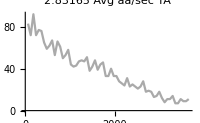
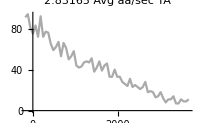
{{2.83165,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = whiteSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TAwhiteTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_wGlobalTimePlot.tif",TAwhiteTimePlot];
TAwhiteSpotCount>>analysisFolder<>"_wGlobalTime.m"
```

#### TL:

```mathematica
TLspotCount = Total[Transpose[TLwhite],{2}]//#[[All,2]]&;
```

```mathematica
name  = "TL";
TLwhiteSpotCount= Transpose[{times,TLspotCount}];(*Combining Time with the # of spots*)
```

{{-178,29},{-118,33},{-58,31},{2,30},{62,31},{122,25},{182,36},{242,28},{302,29},{362,27},{422,21},{482,20},{542,22},{602,22},{662,15},{722,20},{782,18},{842,17},{902,17},{962,17},{1022,14},{1082,11},{1142,15},{1202,17},{1262,15},{1322,14},{1382,17},{1442,15},{1502,16},{1562,15},{1622,9},{1682,13},{1742,13},{1802,10},{1862,9},{1922,9},{1982,8},{2042,11},{2102,7},{2162,6},{2222,8},{2282,10},{2342,10},{2402,9},{2462,5},{2522,8},{2582,5},{2642,7},{2702,5},{2762,3},{2822,8},{2882,2},{2942,4},{3002,6},{3062,3},{3122,3},{3182,3},{3242,4},{3302,5},{3362,3},{3422,4},{3482,3},{3542,4},{3602,3},{3662,3}}

Part::partd: Part specification «1»⟦0,2⟧ is longer than depth of object.

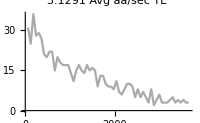
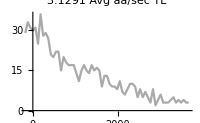
{{3.1291,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = TLwhiteSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TLwhiteTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_wGlobalTimePlot.tif",TLwhiteTimePlot];
TLwhiteSpotCount>>analysisFolder<>"_wGlobalTime.m"
```

#### NT:

```mathematica
name  = "NT";
NTspotCount = Total[Transpose[NTwhite],{2}]//#[[All,2]]&
NTwhiteSpotCount= Transpose[{times,NTspotCount}](*Combining Time with the # of spots*)
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{-178,0},{-118,0},{-58,0},{2,0},{62,0},{122,0},{182,0},{242,0},{302,0},{362,0},{422,0},{482,0},{542,0},{602,0},{662,0},{722,0},{782,0},{842,0},{902,0},{962,0},{1022,0},{1082,0},{1142,0},{1202,0},{1262,0},{1322,0},{1382,0},{1442,0},{1502,0},{1562,0},{1622,0},{1682,0},{1742,0},{1802,0},{1862,0},{1922,0},{1982,0},{2042,0},{2102,0},{2162,0},{2222,0},{2282,0},{2342,0},{2402,0},{2462,0},{2522,0},{2582,0},{2642,0},{2702,0},{2762,0},{2822,0},{2882,0},{2942,0},{3002,0},{3062,0},{3122,0},{3182,0},{3242,0},{3302,0},{3362,0},{3422,0},{3482,0},{3542,0},{3602,0},{3662,0}}

{{-178,0},{-118,0},{-58,0},{2,0},{62,0},{122,0},{182,0},{242,0},{302,0},{362,0},{422,0},{482,0},{542,0},{602,0},{662,0},{722,0},{782,0},{842,0},{902,0},{962,0},{1022,0},{1082,0},{1142,0},{1202,0},{1262,0},{1322,0},{1382,0},{1442,0},{1502,0},{1562,0},{1622,0},{1682,0},{1742,0},{1802,0},{1862,0},{1922,0},{1982,0},{2042,0},{2102,0},{2162,0},{2222,0},{2282,0},{2342,0},{2402,0},{2462,0},{2522,0},{2582,0},{2642,0},{2702,0},{2762,0},{2822,0},{2882,0},{2942,0},{3002,0},{3062,0},{3122,0},{3182,0},{3242,0},{3302,0},{3362,0},{3422,0},{3482,0},{3542,0},{3602,0},{3662,0}}

Part::partd: Part specification {{-178,0},{-118,0},{-58,0},{2,0},{62,0},{122,0},{182,0},{242,0},{302,0},{362,0},{422,0},{482,0},{542,0},{602,0},{662,0},{722,0},{782,0},{842,0},{902,0},{962,0},{1022,0},{1082,0},{1142,0},{1202,0},{1262,0},{1322,0},{1382,0},{1442,0},{1502,0},{1562,0},{1622,0},{1682,0},{1742,0},{1802,0},{1862,0},{1922,0},{1982,0},{2042,0},{2102,0},{2162,0},{2222,0},{2282,0},{2342,0},{2402,0},{2462,0},{2522,0},{2582,0},{2642,0},{2702,0},{2762,0},«15»}⟦0,2⟧ is longer than depth of object.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

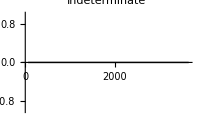
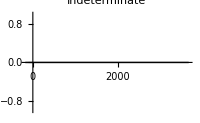
{{Indeterminate,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = NTwhiteSpotCount
myySpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{NTwhiteTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@White,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_wGlobalTimePlot.tif",NTwhiteTimePlot];
NTwhiteSpotCount>>analysisFolder<>"_wGlobalTime.m"
```

### Purple Har translation decay

```mathematica
purple = Table[Import[myPurpleFiles⟦j⟧],{j,1,Length@myPurpleFiles,1}];
TApurple = Table[Import[myTAPurpleFiles⟦j⟧],{j,1,Length@myTAPurpleFiles,1}];
TLpurple = Table[Import[myTLPurpleFiles⟦j⟧],{j,1,Length@myTLPurpleFiles,1}];
NTpurple = Table[Import[myNTPurpleFiles⟦j⟧],{j,1,Length@myNTPurpleFiles,1}];
```

#### ALL:

```mathematica
name = "ALL";
spotCount = Total[Transpose[purple],{2}]//#[[All,2]]&;
purpleSpotCount= Transpose[{times,spotCount}];(*Combining Time with the # of spots*)
```

{{-178,337},{-118,337},{-58,305},{2,303},{62,328},{122,320},{182,322},{242,318},{302,312},{362,308},{422,298},{482,315},{542,299},{602,315},{662,318},{722,318},{782,311},{842,300},{902,315},{962,296},{1022,290},{1082,297},{1142,286},{1202,294},{1262,294},{1322,294},{1382,309},{1442,295},{1502,320},{1562,301},{1622,293},{1682,286},{1742,291},{1802,274},{1862,268},{1922,264},{1982,287},{2042,280},{2102,279},{2162,280},{2222,251},{2282,303},{2342,286},{2402,276},{2462,253},{2522,290},{2582,271},{2642,283},{2702,272},{2762,270},{2822,274},{2882,267},{2942,257},{3002,279},{3062,283},{3122,278},{3182,269},{3242,256},{3302,252},{3362,260},{3422,285},{3482,275},{3542,259},{3602,255},{3662,270}}

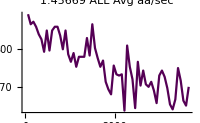
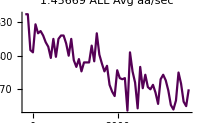
{{1.45669,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = purpleSpotCount
purpleSpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{purpleTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_pGlobalTimePlot.tif",purpleTimePlot];
purpleSpotCount>>analysisFolder<>"_pGlobalTime.m"
```

#### TA:

```mathematica
name = "TA";
TAspotCount = Total[Transpose[TApurple],{2}]//#[[All,2]]&;
TApurpleSpotCount= Transpose[{times,TAspotCount}];(*Combining Time with the # of spots*)
```

{{-178,247},{-118,253},{-58,227},{2,226},{62,239},{122,248},{182,239},{242,242},{302,227},{362,231},{422,229},{482,246},{542,234},{602,231},{662,250},{722,235},{782,243},{842,228},{902,243},{962,232},{1022,218},{1082,229},{1142,216},{1202,226},{1262,219},{1322,228},{1382,230},{1442,228},{1502,250},{1562,227},{1622,226},{1682,215},{1742,222},{1802,209},{1862,209},{1922,203},{1982,220},{2042,219},{2102,218},{2162,211},{2222,195},{2282,231},{2342,221},{2402,216},{2462,203},{2522,229},{2582,218},{2642,228},{2702,209},{2762,206},{2822,213},{2882,201},{2942,209},{3002,236},{3062,223},{3122,221},{3182,218},{3242,200},{3302,198},{3362,205},{3422,228},{3482,221},{3542,208},{3602,207},{3662,220}}

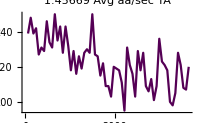
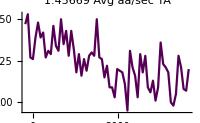
{{1.45669,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = TApurpleSpotCount
purpleSpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TApurpleTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_pGlobalTimePlot.tif",TApurpleTimePlot];
TApurpleSpotCount>>analysisFolder<>"_pGlobalTime.m"
```

#### TL:

```mathematica
name = "TL";
TLspotCount = Total[Transpose[TLpurple],{2}]//#[[All,2]]&;
TLpurpleSpotCount= Transpose[{times,TLspotCount}];(*Combining Time with the # of spots*)
```

{{-178,84},{-118,82},{-58,77},{2,74},{62,86},{122,70},{182,82},{242,75},{302,84},{362,77},{422,66},{482,68},{542,62},{602,82},{662,68},{722,82},{782,65},{842,71},{902,71},{962,63},{1022,70},{1082,66},{1142,70},{1202,68},{1262,74},{1322,65},{1382,79},{1442,67},{1502,70},{1562,74},{1622,67},{1682,68},{1742,69},{1802,64},{1862,58},{1922,60},{1982,67},{2042,61},{2102,61},{2162,69},{2222,55},{2282,72},{2342,65},{2402,60},{2462,50},{2522,61},{2582,52},{2642,55},{2702,62},{2762,63},{2822,61},{2882,66},{2942,48},{3002,43},{3062,60},{3122,57},{3182,51},{3242,56},{3302,54},{3362,55},{3422,57},{3482,53},{3542,51},{3602,48},{3662,50}}

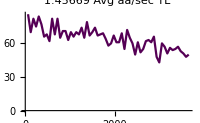
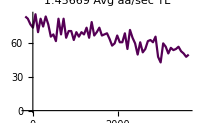
{{1.45669,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = TLpurpleSpotCount
purpleSpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{TLpurpleTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_pGlobalTimePlot.tif",TLpurpleTimePlot];
TLpurpleSpotCount>>analysisFolder<>"_pGlobalTime.m"
```

#### NT:

```mathematica
name = "NT";
spotCount = Total[Transpose[NTpurple],{2}]//#[[All,2]]&;
NTpurpleSpotCount= Transpose[{times,spotCount}];(*Combining Time with the # of spots*)
```

{{-178,6},{-118,2},{-58,1},{2,3},{62,3},{122,2},{182,1},{242,1},{302,1},{362,0},{422,3},{482,1},{542,3},{602,2},{662,0},{722,1},{782,3},{842,1},{902,1},{962,1},{1022,2},{1082,2},{1142,0},{1202,0},{1262,1},{1322,1},{1382,0},{1442,0},{1502,0},{1562,0},{1622,0},{1682,3},{1742,0},{1802,1},{1862,1},{1922,1},{1982,0},{2042,0},{2102,0},{2162,0},{2222,1},{2282,0},{2342,0},{2402,0},{2462,0},{2522,0},{2582,1},{2642,0},{2702,1},{2762,1},{2822,0},{2882,0},{2942,0},{3002,0},{3062,0},{3122,0},{3182,0},{3242,0},{3302,0},{3362,0},{3422,0},{3482,1},{3542,0},{3602,0},{3662,0}}

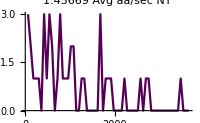
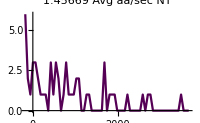
{{1.45669,Avg aa/sec},{-Graphics- -Graphics-}}

```mathematica
spotTime = NTpurpleSpotCount
purpleSpotWeights=Table[If[((Mean@spotTime[[1;;myStartTime,2]]//N)-(StandardDeviation@spotTime[[1;;myStartTime,2]]//N))≥ spotTime[[frame,2]]&&frame≤Flatten[Position[spotTime[[All,2]],Min@spotTime[[All,2]]]][[1]],spotTime[[frame-1,2]]-spotTime[[frame,2]],0],{frame,1,Length@spotTime,1}]; (*Making weights by taking the difference between the previous frame to the next frame if the value is under the lowest # of spots in the pre frames*)
myySpotWeightstempCorr=Table[If[myySpotWeights[[i]]≤0,0,myySpotWeights[[i]]],{i,1,Length@myySpotWeights}];(*If spot # increases or no increase happens will assign a weight of 0*)
myySpotWeightsCorr=ReplacePart[({myySpotWeightstempCorr}//Flatten),{myStartTime}-> 0];(*Adds weight of 0 to first frame and to the myStartTime frame*)
myLTime=AALength/spotTime[[All,1]]//N;(*Dividing the amino acid length by the time after harringtonine was added*)
myWeightedySpotNLTime=myySpotWeightsCorr myLTime;(*Multiplying the weights through*)
{{myAvgAAperSec=Total[myWeightedySpotNLTime[[myStartTime;;myEndTime]]/Total[myySpotWeightsCorr[[myStartTime;;myEndTime ]]]],"Avg aa/sec"},(*Dividing by the max number of spots*)
{NTpurpleTimePlot=spotTime//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}(*All points after adding harringtonine*)
{spotTime[[myStartTime;;myEndTime]]//ListLinePlot[#,PlotStyle->Darker@Purple,PlotLabel->(myAvgAAperSec " Avg aa/sec"name), ImageSize-> 200]&}} (*Area of plot that is being calculated for the aa/sec*)
```

```mathematica
Export[analysisFolder<>"_pGlobalTimePlot.tif",NTpurpleTimePlot];
NTpurpleSpotCount>>analysisFolder<>"_pGlobalTime.m"
```

### View it all...

```mathematica
Row[{"All cells"}]
Row[{purpleTimePlot,whiteTimePlot,yelOnlyTimePlot,yelAllTimePlot}]
```

All cells

-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{"TA cells"}]
Row[{TApurpleTimePlot,TAwhiteTimePlot,TAyelOnlyTimePlot,TAyelAllTimePlot}]
```

TA cells

-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{"TL cells"}]
Row[{TLpurpleTimePlot,TLwhiteTimePlot,TLyelOnlyTimePlot,TLyelAllTimePlot}]
```

TL cells

-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{"NT cells"}]
Row[{NTpurpleTimePlot,NTwhiteTimePlot,NTyelOnlyTimePlot,NTyelAllTimePlot}]
```

NT cells

-Graphics--Graphics--Graphics--Graphics-

## Bootstrapping the datasets:

### Reading In BS Parameters:

```mathematica
sampleSize = Length@onlyYellowSpots  
(* sampleSize usually uses the same # as sample size, in my case, number of cells*) 
repetitions = 30  (* this is repetition of finding the mean of BS data needs to be at least 20 or 30*)
```

22

30

### BS for Only Yellow Spots:

```mathematica
onlyYellow//Dimensions
```

{22,65,2}

```mathematica
onlyYellowSpots = onlyYellow[[All,All,2]];
onlyYellowSpots;
```

{{8,5,5,5,5,7,5,4,4,1,6,4,4,3,5,3,4,5,4,4,5,1,5,5,4,2,3,2,3,4,4,2,3,2,2,2,2,0,1,3,2,1,2,1,1,3,0,0,0,0,1,0,1,0,0,1,1,1,1,1,1,0,1,1,2},{2,3,5,4,3,3,4,3,4,2,3,6,3,5,7,7,5,6,4,2,3,1,4,3,1,1,2,3,3,2,3,0,3,3,4,2,1,3,0,0,1,1,3,2,2,2,3,1,2,3,3,1,1,1,1,0,1,1,2,0,1,1,5,1,0},{5,13,9,6,6,4,7,5,7,9,6,10,9,8,6,4,2,7,3,6,4,1,6,5,4,5,5,2,3,2,3,1,3,5,3,3,3,2,4,3,1,3,5,2,3,3,4,0,2,1,2,0,3,0,0,2,3,2,0,2,0,2,1,1,0},{20,18,19,0,14,15,16,14,14,11,18,12,14,15,13,10,7,7,7,6,6,12,5,5,4,6,0,2,5,1,4,0,3,3,1,3,5,3,2,3,2,3,4,2,2,4,1,2,1,0,2,2,2,0,1,3,1,0,0,1,1,1,0,2,3},{10,5,7,11,10,10,8,7,7,6,6,8,6,11,9,6,8,6,4,7,6,5,6,7,4,6,5,5,8,4,3,7,6,6,2,5,4,3,2,2,2,5,4,4,3,1,2,2,2,1,1,1,1,2,3,4,1,3,3,1,3,2,3,3,2},{2,2,2,2,0,2,2,2,3,2,2,2,2,0,2,2,1,0,1,1,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{5,4,7,6,6,3,3,4,4,2,6,3,4,4,1,4,5,6,2,3,0,4,3,2,0,2,1,1,1,0,1,1,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,2,0,1,0,1,1,0,0,0,0,1,0,0,0,0,0},{4,5,3,9,8,10,13,11,3,7,8,5,6,3,7,4,2,4,2,4,3,3,3,2,0,6,2,1,0,3,1,2,1,2,0,1,1,2,1,1,1,1,1,0,0,1,0,0,2,0,1,0,2,1,1,0,0,0,0,0,1,0,0,0,0},{25,20,16,20,21,25,22,17,20,18,25,25,20,17,18,22,18,14,14,19,12,14,11,8,11,10,11,14,14,14,6,14,8,6,12,6,6,9,8,8,7,0,5,8,3,6,3,5,6,3,2,4,2,3,2,0,2,2,3,2,4,4,5,4,2},{4,4,6,2,1,3,1,2,4,3,1,2,1,0,1,0,1,3,1,1,1,1,1,1,1,0,1,2,1,1,1,2,1,2,1,1,0,1,2,2,0,1,1,0,1,2,0,0,0,1,1,0,1,1,1,1,0,0,1,0,1,1,0,0,0},{5,4,2,2,3,7,6,4,5,2,4,4,5,3,3,1,5,4,2,2,3,1,3,2,2,3,3,2,2,2,3,2,3,2,2,3,2,0,0,1,1,1,0,2,0,0,1,0,1,0,1,2,1,0,2,1,1,2,0,1,1,1,1,1,0},{10,10,11,11,11,9,10,11,9,6,6,9,5,4,8,4,6,7,7,4,4,6,4,5,5,4,7,6,4,5,4,5,5,4,2,2,4,2,1,3,3,2,1,3,1,1,3,2,1,1,1,2,0,1,0,0,0,1,1,0,1,1,0,1,1},{19,13,14,13,13,20,16,15,15,13,10,11,10,11,11,7,9,5,9,10,11,9,10,8,7,7,6,5,6,6,6,4,4,1,5,4,4,5,4,1,3,3,3,4,4,1,3,1,3,2,1,4,2,2,0,1,2,1,1,1,1,1,1,1,0},{15,17,15,16,15,14,12,17,11,11,11,7,12,8,6,6,6,6,8,6,13,4,4,5,7,8,3,4,3,5,6,5,6,3,4,3,3,2,2,3,1,0,2,3,2,1,0,5,1,2,1,1,2,2,2,2,4,2,1,0,3,3,1,1,1},{7,5,4,4,8,7,6,6,2,6,5,4,2,4,5,1,3,5,1,1,1,4,3,2,4,2,4,4,2,0,2,4,1,0,1,1,2,2,2,2,2,1,1,2,3,2,2,1,2,2,1,2,2,0,0,2,0,3,1,3,1,1,2,1,1},{6,6,3,3,4,10,7,7,7,11,6,5,6,5,4,7,6,9,5,4,6,4,6,4,7,2,3,3,3,2,5,3,4,3,1,4,2,1,4,3,2,5,6,2,4,3,0,1,3,2,2,1,1,1,1,1,1,2,1,0,0,1,1,2,1},{6,8,7,6,5,7,5,8,11,7,4,3,4,6,5,4,5,5,5,5,4,5,3,5,2,4,5,5,5,5,4,2,3,6,3,1,6,3,7,1,7,5,4,2,2,4,3,1,4,3,2,6,4,4,1,4,1,4,5,5,2,2,2,3,1},{14,15,12,15,15,7,10,12,6,12,12,14,11,10,6,12,11,10,8,7,9,9,11,3,8,8,4,3,9,7,7,5,9,10,7,5,8,2,4,4,4,4,6,3,4,4,4,3,5,1,4,3,3,5,7,1,2,3,4,2,1,0,1,4,2},{3,1,2,1,5,4,1,2,5,2,2,5,2,2,1,3,1,2,1,1,1,0,2,4,7,1,1,2,3,1,0,1,3,1,0,1,3,0,0,1,1,2,2,2,1,2,1,2,0,1,1,3,0,0,1,0,1,1,1,0,1,0,0,4,0},{7,5,10,10,9,7,7,6,8,8,7,6,6,6,5,4,4,5,5,3,5,4,4,2,1,3,4,5,2,2,3,3,3,0,2,3,3,3,2,1,3,2,1,1,1,2,1,1,2,1,1,1,1,1,2,2,2,2,2,1,2,2,2,0,1},{26,25,19,20,14,19,21,16,22,13,9,8,10,9,5,7,7,8,8,7,6,6,8,4,8,6,7,9,5,7,3,5,6,6,4,4,5,7,4,5,6,2,2,5,2,8,2,5,2,5,2,4,4,5,4,3,4,2,1,4,3,2,3,3,3},{9,7,7,10,7,7,5,15,7,6,7,7,7,2,6,4,5,4,7,3,3,2,5,1,3,5,6,5,4,3,3,5,2,2,1,4,2,6,2,2,4,4,1,4,3,0,3,0,2,2,3,1,1,0,2,0,1,1,0,1,1,0,2,3,1}}

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[onlyYellowSpots[[All,i]]],sampleSize],repetitions ],{i,1,Length@yelOnlySpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS ;
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{10.6818,7.22727,8.31818,7.72727,7.95455,9.5,7.90909,10.3182,8.36364,9.18182,7.59091,10.8636,10.3182,10.9545,8.36364,8.72727,10.8636,9.77273,7.27273,9.27273,9.09091,12.9545,10.2273,10.1364,12.2727,10.9545,9.,11.4545,6.5,8.59091}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{myYelOnlySpotTime ,errorBS}];
```

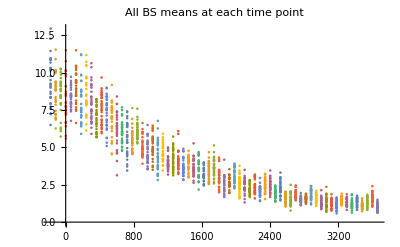

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

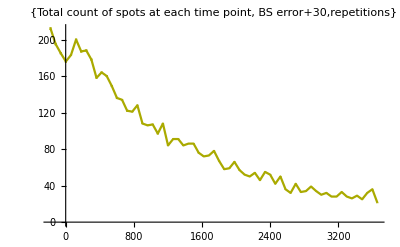

```mathematica
ErrorListPlot[b,PlotStyle->{Darker[Yellow]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```

### BS for All Yellow Spots:

```mathematica
allYellow//Dimensions
```

{22,65,2}

```mathematica
allYellowSpots = allYellow[[All,All,2]];
allYellowSpots;
```

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[allYellowSpots[[All,i]]],sampleSize],repetitions ],{i,1,Length@yelAllSpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{1.47375,1.87211,1.196,1.69242,1.44691,1.20548,1.42185,1.89029,1.24943,1.35059,1.12434,1.22949,1.22882,0.968009,0.918769,1.19824,0.992598,0.895203,1.095,1.20803,1.05847,1.24622,1.15863,0.678107,0.853855,0.844212,0.839274,0.803805,0.747894,0.912716,0.904099,0.754835,0.720529,0.9024,0.796824,0.635955,0.673849,0.689836,0.639678,0.582757,0.617607,0.519874,0.425889,0.490278,0.664764,0.779263,0.48636,0.598002,0.585294,0.479812,0.375005,0.501449,0.395892,0.550743,0.423835,0.278858,0.282652,0.267846,0.490309,0.330102,0.28987,0.256431,0.401077,0.360079,0.308076}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{13.8636,15.0455,13.2727,13.1818,15.6818,12.7273,14.,12.,11.7727,15.1818,13.0455,13.2273,15.7727,11.9091,15.5455,15.2727,13.0455,14.5,14.3182,13.5455,10.6364,15.7273,10.5909,13.6818,13.,11.2273,12.6364,13.1364,14.7273,13.3636}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{yelAllTime ,errorBS}];
```

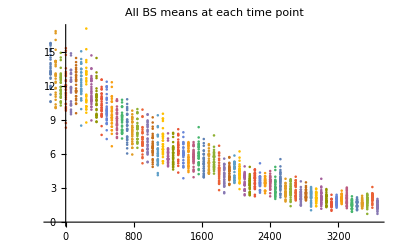

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

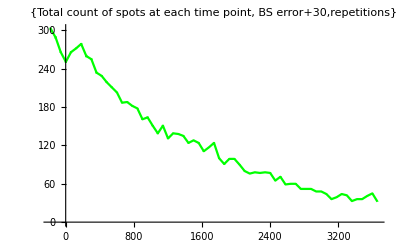

```mathematica
ErrorListPlot[b,PlotStyle->{Green}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```

### BS for White Spots:

```mathematica
white//Dimensions
```

{22,65,2}

```mathematica
white = white[[All,All,2]];
white;
```

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[white[[All,i]]],sampleSize],repetitions ],{i,1,Length@whiteSpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{0.986929,1.11787,0.80773,0.879778,0.871588,0.904829,0.854446,0.67725,1.01148,0.760296,0.675518,0.674172,0.602607,0.704127,0.60848,0.734598,0.677741,0.542978,0.524239,0.556438,0.379428,0.645229,0.445951,0.545272,0.626906,0.495194,0.706596,0.497178,0.562451,0.593105,0.570042,0.396207,0.607331,0.58706,0.313088,0.500425,0.431869,0.464676,0.385214,0.346408,0.29248,0.329025,0.321076,0.309092,0.348578,0.394702,0.307223,0.379437,0.377806,0.397687,0.207419,0.26571,0.174187,0.297072,0.162331,0.138566,0.173695,0.110495,0.24572,0.117616,0.154298,0.185189,0.148582,0.167543,0.160632}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{4.31818,5.31818,3.45455,4.31818,4.5,2.54545,4.5,4.22727,2.31818,3.31818,5.77273,2.95455,4.09091,3.86364,3.04545,5.81818,5.09091,4.95455,6.09091,4.27273,2.90909,4.27273,3.54545,3.45455,3.81818,2.63636,3.95455,4.36364,4.45455,5.18182}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{whiteTime ,errorBS}];
```

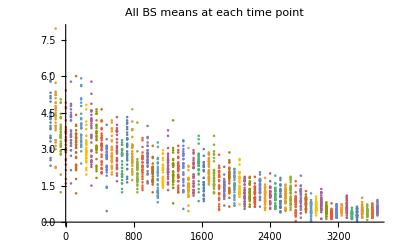

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

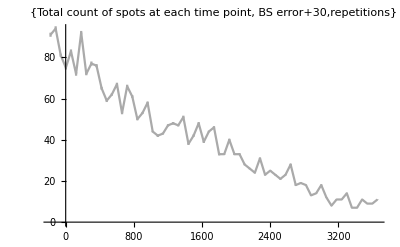

```mathematica
ErrorListPlot[b,PlotStyle->{Darker[White]}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```

### BS for Purple Spots:

```mathematica
purple//Dimensions
```

{22,65,2}

```mathematica
purple = purple[[All,All,2]];
```

```mathematica
(*
DEV: 
I dont think this is right..need one error of all the means instead of the dev of data from each mean 

stdevsBS = Table[Table[StandardDeviation[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}]//Transpose;
errorBS = Table[ErrorBar/@stdevsBS[[i]],{i,1,Length@stdevsBS,1}];
b = Table[Transpose[{meanTimeBS[[i]],errorBS[[i]]}],{i,1,Length@meansBS,1}];
Dimensions/@b
Dimensions/@meansBS
meanTimeBS = Table[Transpose[{Table[times,Length@meansBS][[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];

*)
```

```mathematica
a = Table[Table[Table[RandomChoice[purple[[All,i]]],sampleSize],repetitions ],{i,1,Length@purpleSpotCount,1}];
```

```mathematica
meansBS = N/@Table[Table[Mean[a[[i,j]]],{j,1,Length@a[[i]],1}],{i,1,Length@a,1}];
stdevsBS = N/@StandardDeviation/@meansBS 
errorBS =ErrorBar/@stdevsBS;
Length@meansBS
Length@stdevsBS
```

{4.12527,4.1539,3.53324,2.78547,2.97732,3.75319,3.66152,3.10635,3.18005,2.90694,2.48818,3.73596,3.48332,3.46991,3.18147,4.33107,3.36092,3.48487,3.09454,3.96222,2.4668,3.38366,3.17024,3.57048,3.26978,3.43109,2.72474,3.10206,2.49506,3.81188,3.33623,3.42165,2.79752,3.23162,3.04943,3.08647,3.72838,3.70314,3.34112,2.7966,2.95366,3.49063,3.22522,3.1883,2.96447,2.73833,2.51457,3.45841,2.74142,3.06279,3.61657,2.47502,3.1035,3.54071,3.17298,3.5129,2.99646,2.92408,2.6487,2.9008,3.8811,3.0326,3.1289,2.51594,3.4964}

65

65

```mathematica
meansBS[[1]]
Length/@meansBS
```

{25.0909,12.0909,9.04545,18.6818,13.1818,17.7727,13.8636,18.5,8.81818,15.8182,20.1364,16.6364,14.5909,19.7727,14.7727,12.6364,24.8182,15.,12.5909,13.6818,22.8636,16.7273,19.8182,12.0455,16.5,10.5455,13.2273,18.1818,17.1818,17.6364}

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
c = Table[times,repetitions]//Transpose;
```

```mathematica
Length@c
Length/@c
```

65

{30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30}

```mathematica
repTimes = Table[times,repetitions]//Transpose;
meanTimeBS = Table[Transpose[{repTimes[[i]],meansBS[[i]]}],{i,1,Length@meansBS,1}];
```

```mathematica
b = Transpose[{purpleTime ,errorBS}];
```

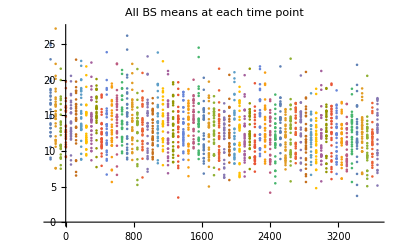

```mathematica
ListPlot[
meanTimeBS,PlotLabel->"All BS means at each time point"]
```

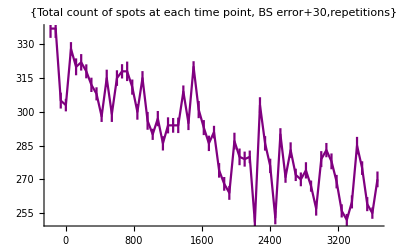

```mathematica
ErrorListPlot[b,PlotStyle->{Purple}, PlotLabel->{"Total count of spots at each time point, BS error" +repetitions ,"repetitions"},Joined->True]
```